Question1

```mathematica
myPlot[func_, xrange_, pltLabel_, pltrange_] :=
Plot[func, xrange, PlotLabel->pltLabel, PlotRange->pltrange, AxesLabel->{"t", "y"}, PlotStyle-> {Thick, Blue}, ExclusionsStyle->Directive[Thick,Blue]]
```

Ramp[-3+t]-Ramp[-2+t]-Ramp[-1+t]+2 Ramp[t]-Ramp[1+t]+UnitStep[t]

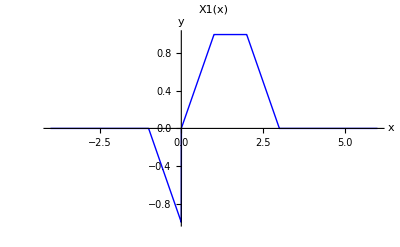

```mathematica
Clear[t, x1]
x1[t_] = UnitStep[t] - Ramp[t+1] + 2Ramp[t] - Ramp[t-1] - Ramp[t-2] + Ramp[t-3]
Plot[x1[t],{t,-4,6}, PlotLabel->"X1(x)", AxesLabel->{"x", "y"}, PlotStyle-> {Thick, Blue}, ExclusionsStyle->Directive[Thick,Blue]]
```

-Ramp[-1+x]+Ramp[x]-UnitStep[-2+x]+UnitStep[-1+x]-2 UnitStep[1+x]+UnitStep[2+x]

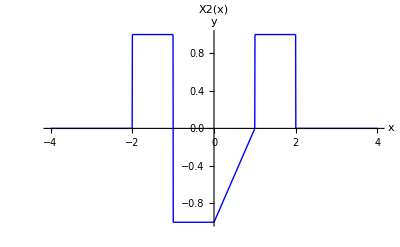

```mathematica
Clear[x, x2]
x2[x_] = UnitStep[x+2] - 2UnitStep[x+1] + Ramp[x] + UnitStep[x-1] - Ramp[x-1] - UnitStep[x-2] 
Plot[x2[x], {x, -4, 4}, PlotLabel->"X2(x)", AxesLabel->{"x", "y"}, PlotStyle-> {Thick, Blue}, ExclusionsStyle->Directive[Thick,Blue]]
```

(Ramp[-3+t]-Ramp[-2+t]-Ramp[-1+t]+2 Ramp[t]-Ramp[1+t]+UnitStep[t]) (-Ramp[-2+t]+Ramp[-1+t]-UnitStep[-3+t]+UnitStep[-2+t]-2 UnitStep[t]+UnitStep[1+t])

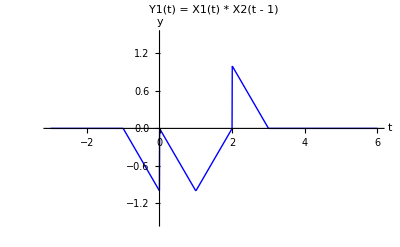

```mathematica
Clear[t, y1]
y1[t_] = x1[t] * x2[t - 1]
myPlot[y1[t], {t, -3, 6}, "Y1(t) = X1(t) * X2(t - 1)", {-1.5, 1.5}]
```

(-Ramp[-1-t]+Ramp[-t]-UnitStep[-2-t]+UnitStep[-1-t]-2 UnitStep[1-t]+UnitStep[2-t]) (Ramp[-4+t]-Ramp[-3+t]-Ramp[-2+t]+2 Ramp[-1+t]-Ramp[t]+UnitStep[-1+t])

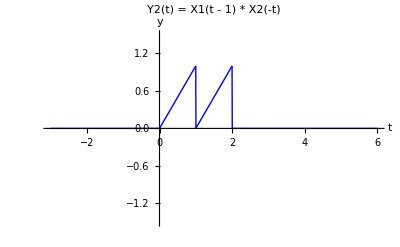

```mathematica
Clear[t, y2]
y2[t_] = x1[t - 1] * x2[-t]
myPlot[y2[t], {t, -3, 6}, "Y2(t) = X1(t - 1) * X2(-t)", {-1.5, 1.5}]
```

Piecewise[{{Ramp[-3+t]-Ramp[-2+t]-Ramp[-1+t]+2 Ramp[t]-Ramp[1+t]+UnitStep[t], -1≤t≤0}, {-Ramp[-3+t]+Ramp[-2+t]-UnitStep[-4+t]+UnitStep[-3+t]-2 UnitStep[-1+t]+UnitStep[t], 0≤t≤3}, {0, True}}]

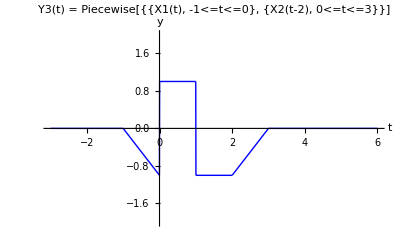

```mathematica
Clear[t, y3]
y3[t_] = Piecewise[{{x1[t], -1<=t<=0}, {x2[t-2], 0<=t<=3}}]
myPlot[y3[t], {t, -3, 6}, "Y3(t) = Piecewise[{{X1(t), -1<=t<=0}, {X2(t-2), 0<=t<=3}}]", {-2, 2}]
```

(-Ramp[8-t]+Ramp[9-t]-UnitStep[7-t]+UnitStep[8-t]-2 UnitStep[10-t]+UnitStep[11-t]) (Ramp[-13+t]-Ramp[-12+t]-Ramp[-11+t]+2 Ramp[-10+t]-Ramp[-9+t]+UnitStep[-10+t])+(-Ramp[6-t]+Ramp[7-t]-UnitStep[5-t]+UnitStep[6-t]-2 UnitStep[8-t]+UnitStep[9-t]) (Ramp[-11+t]-Ramp[-10+t]-Ramp[-9+t]+2 Ramp[-8+t]-Ramp[-7+t]+UnitStep[-8+t])+(-Ramp[4-t]+Ramp[5-t]-UnitStep[3-t]+UnitStep[4-t]-2 UnitStep[6-t]+UnitStep[7-t]) (Ramp[-9+t]-Ramp[-8+t]-Ramp[-7+t]+2 Ramp[-6+t]-Ramp[-5+t]+UnitStep[-6+t])+(-Ramp[2-t]+Ramp[3-t]-UnitStep[1-t]+UnitStep[2-t]-2 UnitStep[4-t]+UnitStep[5-t]) (Ramp[-7+t]-Ramp[-6+t]-Ramp[-5+t]+2 Ramp[-4+t]-Ramp[-3+t]+UnitStep[-4+t])+(Ramp[-5+t]-Ramp[-4+t]-Ramp[-3+t]+2 Ramp[-2+t]-Ramp[-1+t]+UnitStep[-2+t]) (Ramp[1-t]-Ramp[-t]-UnitStep[-1-t]-2 UnitStep[2-t]+UnitStep[3-t]+UnitStep[-t])+(-Ramp[-2-t]+Ramp[-1-t]-UnitStep[-3-t]+UnitStep[-2-t]+UnitStep[1-t]-2 UnitStep[-t]) (Ramp[-3+t]-Ramp[-2+t]-Ramp[-1+t]+2 Ramp[t]-Ramp[1+t]+UnitStep[t])+(-Ramp[-4-t]+Ramp[-3-t]-UnitStep[-5-t]+UnitStep[-4-t]-2 UnitStep[-2-t]+UnitStep[-1-t]) (Ramp[-1+t]-Ramp[t]-Ramp[1+t]+2 Ramp[2+t]-Ramp[3+t]+UnitStep[2+t])+(-Ramp[-6-t]+Ramp[-5-t]-UnitStep[-7-t]+UnitStep[-6-t]-2 UnitStep[-4-t]+UnitStep[-3-t]) (Ramp[1+t]-Ramp[2+t]-Ramp[3+t]+2 Ramp[4+t]-Ramp[5+t]+UnitStep[4+t])+(-Ramp[-8-t]+Ramp[-7-t]-UnitStep[-9-t]+UnitStep[-8-t]-2 UnitStep[-6-t]+UnitStep[-5-t]) (Ramp[3+t]-Ramp[4+t]-Ramp[5+t]+2 Ramp[6+t]-Ramp[7+t]+UnitStep[6+t])+(-Ramp[-10-t]+Ramp[-9-t]-UnitStep[-11-t]+UnitStep[-10-t]-2 UnitStep[-8-t]+UnitStep[-7-t]) (Ramp[5+t]-Ramp[6+t]-Ramp[7+t]+2 Ramp[8+t]-Ramp[9+t]+UnitStep[8+t])+(-Ramp[-12-t]+Ramp[-11-t]-UnitStep[-13-t]+UnitStep[-12-t]-2 UnitStep[-10-t]+UnitStep[-9-t]) (Ramp[7+t]-Ramp[8+t]-Ramp[9+t]+2 Ramp[10+t]-Ramp[11+t]+UnitStep[10+t])

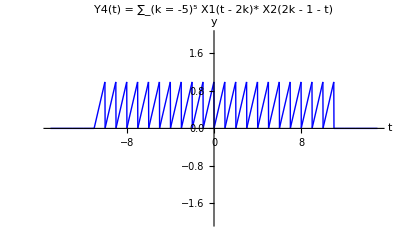

```mathematica
Clear[t, y4]
y4[t_] = ∑_(k=-5)^5 x1[t - 2k]* x2[2k - 1 - t]
myPlot[y4[t], {t, -15, 15}, "Y4(t) = ∑_(k = -5)^5 X1(t - 2k)* X2(2k - 1 - t)", {-2, 2}]
```

```mathematica
Clear[t, x, rect, y5]
rect[t_] = UnitStep[t + 0.5] - UnitStep[t - 0.5]
y5[x_] = rect[y4[x]]
myPlot[y5[t], {t, -15, 15}, "Y5(t) = rect(Y4(t))", {0, 1.5}]
```

-UnitStep[-0.5+t]+UnitStep[0.5+t]

-UnitStep[-0.5+(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])+(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])+(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])+(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])+(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])+(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])+(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])+(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])+(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])+(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])+(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x])]+UnitStep[0.5+(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])+(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])+(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])+(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])+(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])+(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])+(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])+(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])+(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])+(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])+(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x])]

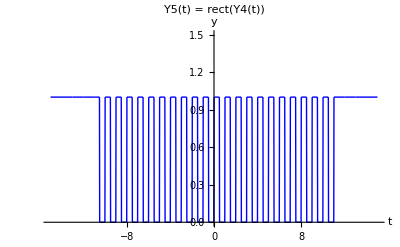

Piecewise[{{1+t, -1≤t≤0}, {1-t, 0≤t≤1}, {0, True}}]

Piecewise[{{1+(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])+(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])+(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])+(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])+(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])+(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])+(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])+(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])+(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])+(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])+(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x]), -1≤(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])+(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])+(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])+(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])+(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])+(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])+(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])+(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])+(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])+(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])+(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x])≤0}, {1-(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])-(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])-(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])-(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])-(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])-(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])-(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])-(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])-(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])-(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])-(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x]), 0≤(-Ramp[8-x]+Ramp[9-x]-UnitStep[7-x]+UnitStep[8-x]-2 UnitStep[10-x]+UnitStep[11-x]) (Ramp[-13+x]-Ramp[-12+x]-Ramp[-11+x]+2 Ramp[-10+x]-Ramp[-9+x]+UnitStep[-10+x])+(-Ramp[6-x]+Ramp[7-x]-UnitStep[5-x]+UnitStep[6-x]-2 UnitStep[8-x]+UnitStep[9-x]) (Ramp[-11+x]-Ramp[-10+x]-Ramp[-9+x]+2 Ramp[-8+x]-Ramp[-7+x]+UnitStep[-8+x])+(-Ramp[4-x]+Ramp[5-x]-UnitStep[3-x]+UnitStep[4-x]-2 UnitStep[6-x]+UnitStep[7-x]) (Ramp[-9+x]-Ramp[-8+x]-Ramp[-7+x]+2 Ramp[-6+x]-Ramp[-5+x]+UnitStep[-6+x])+(-Ramp[2-x]+Ramp[3-x]-UnitStep[1-x]+UnitStep[2-x]-2 UnitStep[4-x]+UnitStep[5-x]) (Ramp[-7+x]-Ramp[-6+x]-Ramp[-5+x]+2 Ramp[-4+x]-Ramp[-3+x]+UnitStep[-4+x])+(Ramp[-5+x]-Ramp[-4+x]-Ramp[-3+x]+2 Ramp[-2+x]-Ramp[-1+x]+UnitStep[-2+x]) (Ramp[1-x]-Ramp[-x]-UnitStep[-1-x]-2 UnitStep[2-x]+UnitStep[3-x]+UnitStep[-x])+(-Ramp[-2-x]+Ramp[-1-x]-UnitStep[-3-x]+UnitStep[-2-x]+UnitStep[1-x]-2 UnitStep[-x]) (Ramp[-3+x]-Ramp[-2+x]-Ramp[-1+x]+2 Ramp[x]-Ramp[1+x]+UnitStep[x])+(-Ramp[-4-x]+Ramp[-3-x]-UnitStep[-5-x]+UnitStep[-4-x]-2 UnitStep[-2-x]+UnitStep[-1-x]) (Ramp[-1+x]-Ramp[x]-Ramp[1+x]+2 Ramp[2+x]-Ramp[3+x]+UnitStep[2+x])+(-Ramp[-6-x]+Ramp[-5-x]-UnitStep[-7-x]+UnitStep[-6-x]-2 UnitStep[-4-x]+UnitStep[-3-x]) (Ramp[1+x]-Ramp[2+x]-Ramp[3+x]+2 Ramp[4+x]-Ramp[5+x]+UnitStep[4+x])+(-Ramp[-8-x]+Ramp[-7-x]-UnitStep[-9-x]+UnitStep[-8-x]-2 UnitStep[-6-x]+UnitStep[-5-x]) (Ramp[3+x]-Ramp[4+x]-Ramp[5+x]+2 Ramp[6+x]-Ramp[7+x]+UnitStep[6+x])+(-Ramp[-10-x]+Ramp[-9-x]-UnitStep[-11-x]+UnitStep[-10-x]-2 UnitStep[-8-x]+UnitStep[-7-x]) (Ramp[5+x]-Ramp[6+x]-Ramp[7+x]+2 Ramp[8+x]-Ramp[9+x]+UnitStep[8+x])+(-Ramp[-12-x]+Ramp[-11-x]-UnitStep[-13-x]+UnitStep[-12-x]-2 UnitStep[-10-x]+UnitStep[-9-x]) (Ramp[7+x]-Ramp[8+x]-Ramp[9+x]+2 Ramp[10+x]-Ramp[11+x]+UnitStep[10+x])≤1}, {0, True}}]

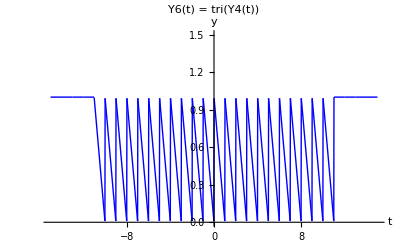

```mathematica
Clear[t, x]
tri[t_] = Piecewise[{{t + 1, -1<=t<=0}, {1 - t, 0<=t<=1}}]

y6[x_] = tri[y4[x]]
myPlot[y6[t], {t, -15, 15}, "Y6(t) = tri(Y4(t))", {0, 1.5}]
```